```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Temp\TESTSIRIUS\VM2D\build\circle200\velPres\output

```mathematica
eigV=Import["eigenV.txt","Table"]//Flatten;
eigP=Import["eigenP.txt","Table"]//Flatten;
```

```mathematica
errV[s_]:=√((Plus@@(eigV[[s+1;;]]))/(Plus@@eigV))
errP[s_]:=√((Plus@@(eigP[[s+1;;]]))/(Plus@@eigP))
```

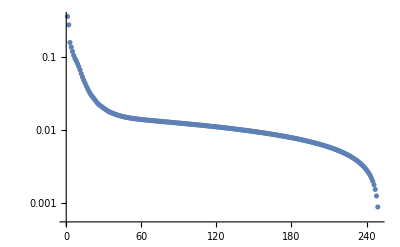

```mathematica
ListLogPlot[Table[errV[s],{s,Length@eigV}],PlotRange->All]
```

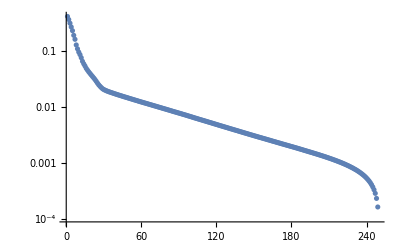

```mathematica
ListLogPlot[Table[errP[s],{s,Length@eigV}],PlotRange->All]
```